# Cavendish

Load and pre-process data

```mathematica
position1data=Import[NotebookDirectory[]<>"day4_position1_data.csv"];
position2data=Import[NotebookDirectory[]<>"day4_position2_data.csv"];
```

```mathematica
(*offset vals*)
```

```mathematica
{offval1,offval2}={9.1517,9.1216};
```

```mathematica
start=2;end=400;
```

```mathematica
{curve1,curve2}={#[[start;;end,-1]],#[[start;;end,-2]]}ᵀ&/@{position1data,position2data};
```

Method-I Fitting with dumped oscillation model

```mathematica
{model,params}={A Exp[-λ t]Cos[ω t+ϕ]+B,{{A,15},{λ,0.001},{ω,0.012},ϕ,{B,30}}};
```

```mathematica
fit1=NonlinearModelFit[curve1,model,params,t,MaxIterations->100];
```

```mathematica
fit2=NonlinearModelFit[curve2,model,params,t,MaxIterations->100];
```

```mathematica
param1=Evaluate@fit1["BestFitParameters"];
param2=Evaluate@fit2["BestFitParameters"];
```

```mathematica
{Subscript[σ, ω1],Subscript[σ, B1]}=Part[First[fit1[{"ParameterErrors"}]],{3,5}]
```

{8.35197×10^-7,0.00299906}

```mathematica
{Subscript[σ, ω2],Subscript[σ, B2]}=Part[First[fit2[{"ParameterErrors"}]],{3,5}]
```

{2.53344×10^-6,0.00511381}

```mathematica
fit1[{"ParameterTable"}]//First
```

| Estimate | Standard Error | t-Statistic | P-Value
A | -16.5432 | 0.00976245 | -1694.58 | 0.
λ | 0.000299712 | 9.27725×10^-7 | 323.061 | 0.
ω | 0.0125738 | 8.35197×10^-7 | 15054.9 | 0.
ϕ | 0.537226 | 0.000519459 | 1034.2 | 0.
B | 31.3377 | 0.00299906 | 10449.2 | 0.

```mathematica
fit2[{"ParameterTable"}]//First
```

| Estimate | Standard Error | t-Statistic | P-Value
A | 9.98778 | 0.015527 | 643.25 | 0.
λ | 0.000269804 | 2.36035×10^-6 | 114.307 | 3.16603×10^-304
ω | 0.0125537 | 2.53344×10^-6 | 4955.21 | 0.
ϕ | 1.60345 | 0.00155875 | 1028.68 | 0.
B | 27.8822 | 0.00511381 | 5452.33 | 0.

```mathematica
{c1,c2}={Interpreter["ComputedColor"]["RGB 255 205 0"],Interpreter["ComputedColor"]["RGB 0 215 160"]}
```

{RGBColor[1, Rational[41, 51], 0],RGBColor[0, Rational[43, 51], Rational[32, 51]]}

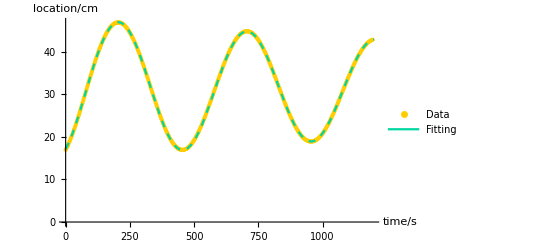

```mathematica
Legended[Show[ListPlot[curve1,PlotStyle->{c1,PointSize[Small]}],
Plot[model/.param1,{t,0,3 end},PlotStyle->{Dashed,c2}],
AxesLabel->{"time/s","location/cm"},AxesStyle->Black,BaseStyle->{FontSize->14}],
LineLegend[{c1,c2},{"Data","Fitting"},Joined->{False,True}]]
```

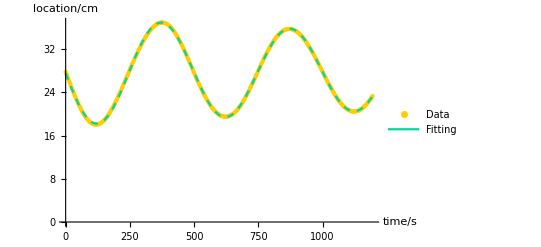

```mathematica
Legended[Show[ListPlot[curve2,PlotStyle->{c1,PointSize[Small]}],Plot[model/.param2,{t,0,3 end},PlotStyle->{Dashed,c2}],AxesLabel->{"time/s","location/cm"},AxesStyle->Black,BaseStyle->{FontSize->14}],
LineLegend[{c1,c2},{"Data","Fitting"},Joined->{False,True}]]
```

Calculate gravitational constant

```mathematica
ΔS=Quantity[Abs[(B/.param1)+offval1-(B/.param2)-offval2],"cm"]
```

3.48566 cm

```mathematica
T=Quantity[4π/((ω/.param1)+(ω/.param2)),"s"]
```

500.104 s

```mathematica
{r,d,b,m}={Quantity[9.55,"mm"],Quantity[50,"mm"],Quantity[42.2,"mm"],Quantity[1.5,"kg"]};
```

```mathematica
Subscript[L, arr]={134.5,134.7,135.0,135.5,135.3,135.6,135.0,135.2};
```

```mathematica
{L,Subscript[σ, L]}=Quantity[{Mean@Subscript[L, arr],2*StandardDeviation@Subscript[L, arr]},"cm"]
```

{135.1 cm,0.755929 cm}

```mathematica
G=π^2 ΔS b^2(d^2+2/5 r^2)/(T^2 m L d)//UnitConvert
```

6.13203×10^-11 m^3/(kg s^2)

Correction and error

```mathematica
β=b^3/((b^2+4 d^2)^(3/2))
```

0.0587723

```mathematica
Subscript[G, 0]=G/(1-β)
```

6.51493×10^-11 m^3/(kg s^2)

```mathematica
Subscript[σ, S-def]=0.1(*cm max presion of the metric scale*);
Subscript[σ, ΔS]=Quantity[√((Subscript[σ, B1]+Subscript[σ, B2])^2+(Subscript[σ, S-def])^2),"cm"]
```

0.100329 cm

```mathematica
Subscript[σ, T-def]=10^-6;(*the computer is precise enough for timing*)
Subscript[σ, T]=T √(Max[ Subscript[σ, ω1]/(ω/.param1),Subscript[σ, ω2]/(ω/.param2)]^2+(Subscript[σ, T-def])^2)
```

0.100926 s

```mathematica
Subscript[σ, L-def]=Quantity[0.5,"mm"];
Subscript[σ, L]=√((Subscript[σ, L])^2+Subscript[σ, L-def]^2)
```

7.57581 mm

```mathematica
Subscript[δ, m]=Quantity[10,"g"]
```

10 g

```mathematica
Subscript[σ, G0]=Subscript[G, 0] √((Subscript[σ, ΔS]/ΔS)^2+4(Subscript[σ, T]/T)^2+(Subscript[σ, L]/L)^2+(Subscript[δ, m]/m)^2)
```

1.95939×10^-12 m^3/(kg s^2)

```mathematica
Quantity[, "GravitationalConstant"]//UnitConvert
```

6.674×10^-11 m^3/(kg s^2)

```mathematica
Abs@(Subscript[G, 0]-Quantity[, "GravitationalConstant"])
```

0.0238465 G